MessageName::messg: RxnsysToSrxnsys::usage cannot be set to  Produces reactions in srxn[[reaction index],{x1,x2},{x3},k] format ( ). Removes any other statements.   reaction index is 1-based reaction structured system. It must be set to a string.

a[tmax]: 3.99999859848042

b[tmax]: 4.000001382550143

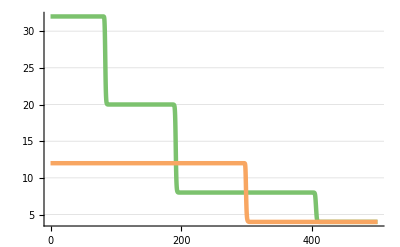

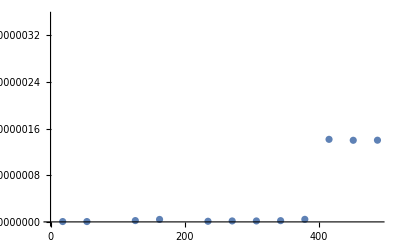

```mathematica
Get[ParentDirectory[NotebookDirectory[]]<>"/packages/init.m"]
Get[NotebookDirectory[]<>"/gcd.m"]

rsys=GCDRsys[32,12];
tmax=500;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
r0tmax=NumberForm[EvaluateRxnAtPoint[sol,a,tmax], Infinity];
r1tmax=NumberForm[EvaluateRxnAtPoint[sol,b,tmax], Infinity];
Print["a[tmax]: " <> ToString[r0tmax]];
Print["b[tmax]: " <> ToString[r1tmax]];
PlotForPaper[Evaluate[{a[t],b[t]}/.sol], tmax]
(*Plot[Evaluate[{a[t],b[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{Magenta, Orange},Ticks->{Range[0,tmax,100],Automatic}]*)
errorMap=EvaluateError[rsys, tmax];
aErrorList=errorMap[a]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[aErrorList,Ticks->{Range[0,tmax,100],Automatic}]
```